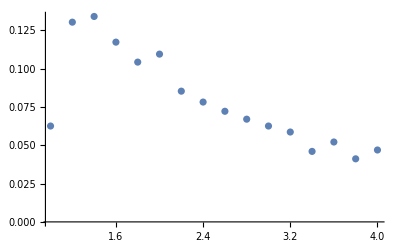

```mathematica
b11={{1,0/(1×32)}, {1.2,2/(1.2×32)},{1.4,7/(1.4×32)},{1.6,14/(1.6×32)}, {1.8,21/(1.8×32)},{2,27/(2×32)},{2.2,34/(2.2×32)},{2.4,41/(2.4×32)},{2.6,48/(2.6×32)},{2.8,54/(2.8×32)},{3,61/(3×32)},{3.2,67/(3.2×32)},{3.4,74/(3.4×32)},{3.6,80/(3.6×32)},{3.8,87/(3.8×32)},{4,93/(4×32)}};
b12={{1,2/(1×32)}, {1.2,7/(1.2×32)},{1.4,13/(1.4×32)},{1.6,20/(1.6×32)}, {1.8,27/(1.8×32)},{2,34/(2×32)},{2.2,40/(2.2×32)},{2.4,47/(2.4×32)},{2.6,54/(2.6×32)},{2.8,60/(2.8×32)},{3,67/(3×32)},{3.2,73/(3.2×32)},{3.4,79/(3.4×32)},{3.6,86/(3.6×32)},{3.8,92/(3.8×32)},{4,99/(4×32)}};
b1=b12-b11*Table[{0,1},{i,0,15}];
ListPlot[{b1}]
```

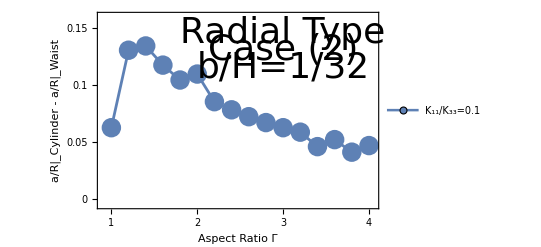

```mathematica
ListPlot[{b1},PlotStyle->{Thickness[0.005]},PlotMarkers->{Graphics[{Disk[]},ImageSize->20]},Joined->{True, True,True, True}, Frame->{True, True, True, True}, FrameTicks->{{{0,0.05,0.1,0.15},None},{{0,1,2,3,4},None}}, PlotRange->{{0.9,4.05},{-0.005,0.16}},FrameLabel->{{"a/R|_Cylinder - a/R|_Waist", None},{"Aspect Ratio Γ", None}},FrameTicksStyle->Directive[Black,36],FrameStyle->Thickness[0.005],LabelStyle->Directive[Black,36],PlotLegends->Placed[PointLegend[{"K_11/K_33=0.1"},LegendMarkers->{{Graphics[Disk[]],20}}],{Left, Bottom}],Epilog->{Text[Style["Radial Type",Directive[Black,36]],{3.0,0.145}],Text[Style["Case (2)",Directive[Black,36]],{3.0,0.13}],
Text[Style["b/H=1/32",Directive[Black,36]],{3.0,0.115}]}]
```